## SimInterpolate-example.nb

Example Cellzilla2D notebook
GPL License applies.
See http://xlr8r.info and http://cellzilla.info for further details.

Cellzilla2D (3.0.0 (10-Nov-2012)) loaded Sat 10 Nov 2012 19:14:09
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

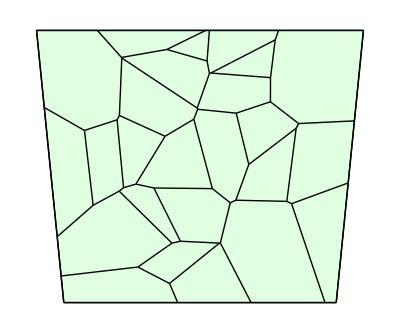

```mathematica
<<Cellzilla2D.m
w=TemplateRandom[25, {{0,0}, {10,0}, {11, 10}, {-1, 10}}];
ShowTissue[w]
```

## Set up a model and run a simulation

```mathematica
n=NTissueCells[w]; 
net={{∅⇄A,k1, k2},{2 A+B->3 A,k3},{A->B,k4}};
parameters={k1-> .1, k2-> .1, k3-> .1 ,k4-> .3};
ic[i_]:={A[i]->RandomReal[{0,5}],B[i]->RandomReal[{0,5}]};
myic=Flatten[ic/@Range[n]]
```

{A[1]→2.45499,B[1]→2.64314,A[2]→4.53776,B[2]→1.54745,A[3]→1.36596,B[3]→1.32281,A[4]→1.63393,B[4]→3.23441,A[5]→1.58607,B[5]→3.10184,A[6]→0.442119,B[6]→1.9087,A[7]→1.86667,B[7]→2.86883,A[8]→0.787872,B[8]→3.23844,A[9]→0.0651613,B[9]→2.38658,A[10]→1.26429,B[10]→3.23609,A[11]→0.52244,B[11]→1.62583,A[12]→3.80754,B[12]→1.74385,A[13]→0.430159,B[13]→4.75054,A[14]→3.27904,B[14]→4.6687,A[15]→0.665241,B[15]→2.52583,A[16]→0.286418,B[16]→2.47285,A[17]→2.56386,B[17]→0.727239,A[18]→1.33976,B[18]→0.689137,A[19]→0.56501,B[19]→3.32931,A[20]→3.34581,B[20]→0.601234,A[21]→1.29647,B[21]→0.83151,A[22]→4.13092,B[22]→0.718387,A[23]→4.27348,B[23]→4.9498,A[24]→2.07089,B[24]→2.99874,A[25]→3.27846,B[25]→3.62761}

```mathematica
bignet=CelleratorNetwork[w, "Reactions"-> net,"Diffusion"-> {{A, DA}, {B,DB}}];
```

25 Cells.

4 internal reactions in each cell.

100 intracellular reactions.

240 diffusion reactions.

340 total reactions.

```mathematica
sim=RunSim[bignet/.{DB->.05, DA-> .1},parameters,myic,{0,50}]
```

{A[1]→InterpolatingFunction[{{0.,50.}},<>],A[2]→InterpolatingFunction[{{0.,50.}},<>],A[3]→InterpolatingFunction[{{0.,50.}},<>],A[4]→InterpolatingFunction[{{0.,50.}},<>],A[5]→InterpolatingFunction[{{0.,50.}},<>],A[6]→InterpolatingFunction[{{0.,50.}},<>],A[7]→InterpolatingFunction[{{0.,50.}},<>],A[8]→InterpolatingFunction[{{0.,50.}},<>],A[9]→InterpolatingFunction[{{0.,50.}},<>],A[10]→InterpolatingFunction[{{0.,50.}},<>],A[11]→InterpolatingFunction[{{0.,50.}},<>],A[12]→InterpolatingFunction[{{0.,50.}},<>],A[13]→InterpolatingFunction[{{0.,50.}},<>],A[14]→InterpolatingFunction[{{0.,50.}},<>],A[15]→InterpolatingFunction[{{0.,50.}},<>],A[16]→InterpolatingFunction[{{0.,50.}},<>],A[17]→InterpolatingFunction[{{0.,50.}},<>],A[18]→InterpolatingFunction[{{0.,50.}},<>],A[19]→InterpolatingFunction[{{0.,50.}},<>],A[20]→InterpolatingFunction[{{0.,50.}},<>],A[21]→InterpolatingFunction[{{0.,50.}},<>],A[22]→InterpolatingFunction[{{0.,50.}},<>],A[23]→InterpolatingFunction[{{0.,50.}},<>],A[24]→InterpolatingFunction[{{0.,50.}},<>],A[25]→InterpolatingFunction[{{0.,50.}},<>],B[1]→InterpolatingFunction[{{0.,50.}},<>],B[2]→InterpolatingFunction[{{0.,50.}},<>],B[3]→InterpolatingFunction[{{0.,50.}},<>],B[4]→InterpolatingFunction[{{0.,50.}},<>],B[5]→InterpolatingFunction[{{0.,50.}},<>],B[6]→InterpolatingFunction[{{0.,50.}},<>],B[7]→InterpolatingFunction[{{0.,50.}},<>],B[8]→InterpolatingFunction[{{0.,50.}},<>],B[9]→InterpolatingFunction[{{0.,50.}},<>],B[10]→InterpolatingFunction[{{0.,50.}},<>],B[11]→InterpolatingFunction[{{0.,50.}},<>],B[12]→InterpolatingFunction[{{0.,50.}},<>],B[13]→InterpolatingFunction[{{0.,50.}},<>],B[14]→InterpolatingFunction[{{0.,50.}},<>],B[15]→InterpolatingFunction[{{0.,50.}},<>],B[16]→InterpolatingFunction[{{0.,50.}},<>],B[17]→InterpolatingFunction[{{0.,50.}},<>],B[18]→InterpolatingFunction[{{0.,50.}},<>],B[19]→InterpolatingFunction[{{0.,50.}},<>],B[20]→InterpolatingFunction[{{0.,50.}},<>],B[21]→InterpolatingFunction[{{0.,50.}},<>],B[22]→InterpolatingFunction[{{0.,50.}},<>],B[23]→InterpolatingFunction[{{0.,50.}},<>],B[24]→InterpolatingFunction[{{0.,50.}},<>],B[25]→InterpolatingFunction[{{0.,50.}},<>]}

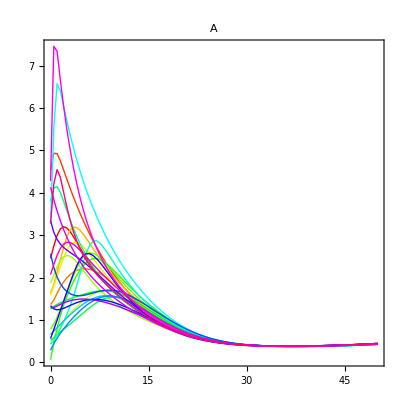
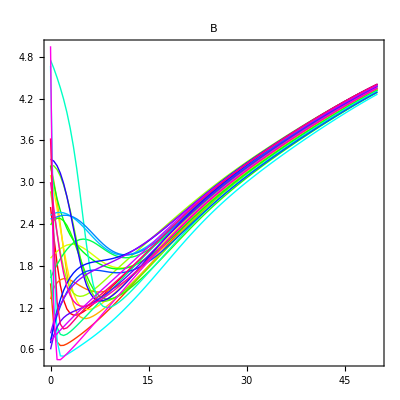

```mathematica
SimPlot[sim]
```

## Use Sim Interpolate to get all values of A at a specific time

```mathematica
SimInterpolate[sim, A, 10]
```

{1.61951,2.00804,1.8259,1.96759,1.80163,1.66211,1.3947,2.06014,2.11724,1.64744,1.53693,1.61448,2.27687,2.54114,1.54645,1.55149,1.68956,1.39744,1.86168,1.68912,1.34067,1.49464,1.89831,1.77724,1.63031}

## Use SimInterpolate to Make a table of Values

```mathematica
TableForm[Prepend[SimInterpolate[sim, A, #], #]&/@Range[0,10,1]]
```

0 | 2.45499 | 4.53776 | 1.36596 | 1.63393 | 1.58607 | 0.442119 | 1.86667 | 0.787872 | 0.0651613 | 1.26429 | 0.52244 | 3.80754 | 0.430159 | 3.27904 | 0.665241 | 0.286418 | 2.56386 | 1.33976 | 0.56501 | 3.34581 | 1.29647 | 4.13092 | 4.27348 | 2.07089 | 3.27846
1 | 2.99317 | 4.92316 | 1.63349 | 2.11705 | 2.02612 | 0.730886 | 2.25424 | 1.0652 | 0.809957 | 1.36961 | 0.651487 | 4.14923 | 0.651809 | 6.57242 | 0.816504 | 0.574435 | 2.01418 | 1.24155 | 0.997678 | 2.90169 | 1.33104 | 3.57237 | 7.33537 | 2.52337 | 4.54737
2 | 3.20166 | 4.53817 | 1.8992 | 2.72235 | 2.47134 | 0.964144 | 2.49332 | 1.44173 | 1.34634 | 1.44237 | 0.781616 | 3.8015 | 0.960152 | 6.04471 | 0.97583 | 0.791939 | 1.74886 | 1.2771 | 1.44308 | 2.71198 | 1.4045 | 3.13347 | 6.03975 | 2.79254 | 4.01328
3 | 3.08323 | 4.1047 | 2.07308 | 3.12342 | 2.76673 | 1.15554 | 2.50426 | 1.84298 | 1.73898 | 1.50232 | 0.908901 | 3.36363 | 1.33621 | 5.36293 | 1.1254 | 0.978866 | 1.62044 | 1.3453 | 1.88536 | 2.59335 | 1.45704 | 2.7829 | 5.01511 | 2.82821 | 3.34949
4 | 2.83828 | 3.70585 | 2.17137 | 3.17824 | 2.83124 | 1.31822 | 2.36487 | 2.22161 | 2.04864 | 1.55632 | 1.03685 | 2.97547 | 1.81344 | 4.77819 | 1.26068 | 1.14425 | 1.57512 | 1.40954 | 2.27997 | 2.4887 | 1.48647 | 2.49899 | 4.22287 | 2.7221 | 2.86552
5 | 2.57731 | 3.34577 | 2.2073 | 3.02529 | 2.72941 | 1.45597 | 2.17043 | 2.48692 | 2.27917 | 1.60551 | 1.16734 | 2.64847 | 2.35695 | 4.2763 | 1.37773 | 1.28676 | 1.58175 | 1.45645 | 2.52323 | 2.37502 | 1.49494 | 2.26551 | 3.60293 | 2.56332 | 2.52791
6 | 2.33618 | 3.02114 | 2.19441 | 2.80317 | 2.55268 | 1.56641 | 1.97403 | 2.58268 | 2.41665 | 1.64741 | 1.29545 | 2.37384 | 2.76817 | 3.84147 | 1.47179 | 1.40358 | 1.61698 | 1.48244 | 2.56381 | 2.24775 | 1.48626 | 2.0692 | 3.11149 | 2.3942 | 2.282
7 | 2.12221 | 2.72829 | 2.14136 | 2.57255 | 2.35466 | 1.64463 | 1.7963 | 2.53481 | 2.44849 | 1.67732 | 1.40763 | 2.14108 | 2.86917 | 3.45991 | 1.53784 | 1.49101 | 1.66016 | 1.48769 | 2.45382 | 2.11058 | 1.46419 | 1.89987 | 2.71632 | 2.22868 | 2.08708
8 | 1.93392 | 2.46383 | 2.0556 | 2.35377 | 2.15873 | 1.68653 | 1.642 | 2.40332 | 2.38686 | 1.68966 | 1.48939 | 1.94131 | 2.73636 | 3.12064 | 1.57223 | 1.54536 | 1.69347 | 1.47376 | 2.27053 | 1.96894 | 1.43148 | 1.75052 | 2.39341 | 2.07034 | 1.91996
9 | 1.76764 | 2.22467 | 1.94713 | 2.15209 | 1.97357 | 1.69128 | 1.5094 | 2.2361 | 2.26586 | 1.68014 | 1.53274 | 1.76756 | 2.51349 | 2.81611 | 1.57424 | 1.565 | 1.70492 | 1.44283 | 2.0648 | 1.8274 | 1.38991 | 1.6165 | 2.12505 | 1.91987 | 1.76939
10 | 1.61951 | 2.00804 | 1.8259 | 1.96759 | 1.80163 | 1.66211 | 1.3947 | 2.06014 | 2.11724 | 1.64744 | 1.53693 | 1.61448 | 2.27687 | 2.54114 | 1.54645 | 1.55149 | 1.68956 | 1.39744 | 1.86168 | 1.68912 | 1.34067 | 1.49464 | 1.89831 | 1.77724 | 1.63031